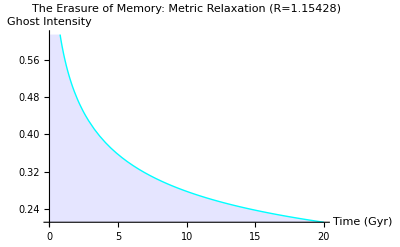

```mathematica
(*The Vanguard Audit:Metric Relaxation Time*)ClearAll["Global`*"];
R=1.15428;
a0=1.0;
offVal=6.0;

(*The Decay Function:s represents cosmic time in Giga-years*)
GhostDecay[s_]:=Module[{intensity},(*The anomaly residue dissipates as 1/sqrt(s) based on heat kernel*)intensity=(R*Sqrt[a0])/(1+Sqrt[s]);
intensity];

Plot[GhostDecay[s],{s,0,20},PlotStyle->{Thick,Cyan},AxesLabel->{"Time (Gyr)","Ghost Intensity"},PlotLabel->"The Erasure of Memory: Metric Relaxation (R=1.15428)",Filling->Axis,FillingStyle->Directive[Opacity[0.1],Blue]]
```